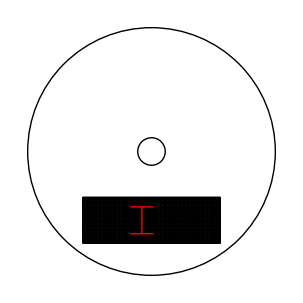

```mathematica
Graphics[{Circle[{0,0},0.27],Circle[{0,0},0.03],EdgeForm[Black],FaceForm[None],Module[{length=0.3,width=0.1,r=0.15,angle=-Pi/2,center,rect,nx=36,ny=12,gridLines,dotPoints,topLine,midLine,bottomLine},center=r*{Cos[angle],Sin[angle]};
rect=Rectangle[{-length/2,-width/2},{length/2,width/2}];
(*Solid grid lines*)gridLines=Join[Table[Line[{{x,-width/2},{x,width/2}}],{x,-length/2,length/2,length/nx}],Table[Line[{{-length/2,y},{length/2,y}}],{y,-width/2,width/2,width/ny}]];
(*Points at square centers*)dotPoints=Table[Point[{-length/2+(i+0.5)*length/nx,-width/2+(j+0.5)*width/ny}],{i,0,nx-1},{j,0,ny-1}];
(*Coordinates for "I" shape*)(*Top horizontal line from i=12 to i=18 at row j=9*)topLine=Table[{-length/2+(i+0.5)*length/nx,-width/2+(9+0.5)*width/ny},{i,12,18}];
(*Bottom horizontal line from i=12 to i=18 at row j=2*)bottomLine=Table[{-length/2+(i+0.5)*length/nx,-width/2+(2+0.5)*width/ny},{i,12,18}];
(*Vertical line from j=2 to j=9 at column i=15*)midLine=Table[{-length/2+(15+0.5)*length/nx,-width/2+(j+0.5)*width/ny},{j,2,9}];
GeometricTransformation[{rect,gridLines,Black,PointSize[Small],dotPoints,Red,Thick,Line[topLine],Line[midLine],Line[bottomLine]},TranslationTransform[center]]]}]
```

```mathematica
Manipulate[Module[{l1=0.4,l2=0.5,x1,y1,x2,y2,z},x1=l1 Cos[θ1];
y1=l1 Sin[θ1];
x2=x1+l2 Cos[θ1+θ2];
y2=y1+l2 Sin[θ1+θ2];
z=-d3;
Graphics3D[{Thick,Blue,Line[{{0,0,0},{x1,y1,0}}],Green,Line[{{x1,y1,0},{x2,y2,0}}],Red,Line[{{x2,y2,0},{x2,y2,z}}],Black,Sphere[{0,0,0},0.05],Black,Sphere[{x1,y1,0},0.05],Black,Sphere[{x2,y2,0},0.05],Black,Sphere[{x2,y2,z},0.05]},Axes->True,AxesOrigin->{0,0,0},Boxed->False,PlotRange->{{-1,1},{-1,1},{0.1,-0.5}},SphericalRegion->True]],{{θ1,0,"Theta 1 (°)"},-180 Degree,180 Degree},{{θ2,0,"Theta 2 (°)"},-180 Degree,180 Degree},{{d3,0,"Prismatic Z (units)"},0,4}]
```

```mathematica
Manipulate[Module[{l1=6,l2=4,jointSize=0.2,baseHeight=1.9,armThickness=0.3,x1,y1,x2,y2,z,base,arm1,arm2,verticalSlide},x1=l1 Cos[θ1];
y1=l1 Sin[θ1];
x2=x1+l2 Cos[θ1+θ2];
y2=y1+l2 Sin[θ1+θ2];
z=-d3;
base={Gray,Cylinder[{{0,0,baseHeight},{0,0,0}},1]};
arm1={Blue,Cylinder[{{0,0,baseHeight},{x1,y1,baseHeight}},armThickness]};
arm2={Green,Cylinder[{{x1,y1,baseHeight},{x2,y2,baseHeight}},armThickness]};
verticalSlide={Red,Cylinder[{{x2,y2,baseHeight},{x2,y2,z+2}},armThickness*0.6]};
Graphics3D[{base,arm1,arm2,verticalSlide,Black,Sphere[{0,0,baseHeight},jointSize],Black,Sphere[{x1,y1,baseHeight},jointSize],Black,Sphere[{x2,y2,baseHeight},jointSize],Black,Sphere[{x2,y2,baseHeight},jointSize]},Axes->True,AxesLabel->{"X","Y","Z"},AxesOrigin->{0,0,0},Boxed->False,PlotRange->{{-12,12},{-12,12},{-6,2}},SphericalRegion->True,Lighting->"Neutral",ViewPoint->{1.2,-2.4,1.5},ImageSize->500 ]],{{θ1,0,"Theta 1 (°)"},-180 Degree,180 Degree},{{θ2,0,"Theta 2 (°)"},-180 Degree,180 Degree},{{d3,0,"Z Prismatic (units)"},0,5}]
```